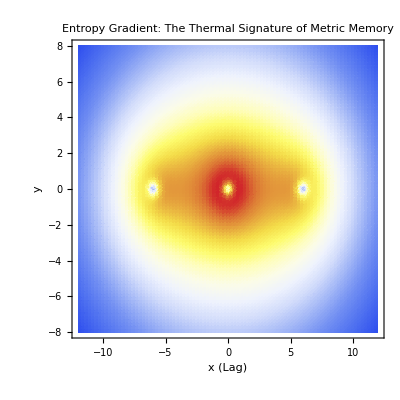

```mathematica
(*Vanguard Audit:Thermodynamic Entropy of the Metric Memory*)ClearAll["Global`*"];
R=1.15428;a0=1.0;offVal=6.0;softening=0.05;

(*Define the Audit Potential (The Informational Density)*)
AuditPotential[x_,y_]:=Module[{rGas,rA,rB},rGas=Sqrt[x^2+y^2+softening];
rA=Sqrt[(x-offVal)^2+y^2+softening];
rB=Sqrt[(x+offVal)^2+y^2+softening];
(1.0/rGas+(R*Sqrt[a0])*Log[rGas])+(1.2/rA+(R*Sqrt[1.2*a0])*Log[rA])+(1.2/rB+(R*Sqrt[1.2*a0])*Log[rB])];

(*Entropy is inversely proportional to the structured Audit potential*)
MetricEntropy[x_,y_]:=-Log[AuditPotential[x,y]+0.1];

(*1. Visualize the Entropy'Cooling'*)
DensityPlot[MetricEntropy[x,y],{x,-12,12},{y,-8,8},ColorFunction->"TemperatureMap",PlotPoints->90,PlotRange->All,PlotLabel->"Entropy Gradient: The Thermal Signature of Metric Memory",FrameLabel->{"x (Lag)","y"}]
```